## Formula derivation

The system contains a certain number of two-level giant atoms,  each of them couples to a 1D waveguide through multiple connection points. The atom  is labelled by i. The coordinates of the connecting points are x_im .

Hamiltonian of the whole system:

H=∑_i (ω_i-ⅈ γ_i/2)σ_i^†σ_i^-
    +∫ⅆx{c_R^†(x)(-ⅈv_g∂/(∂x))c_R(x)+c_L^†(x)(ⅈv_g∂/(∂x))c_L(x)}
    +∫ⅆx∑_i ∑_m V_im δ(x-x_(i m))[c_R^†(x)σ_i^-+c_R(x)σ_i^†+c_L^†(x)σ_i^-+c_L(x)σ_i^†]

In the single-photon sector, the eigen state of the system could be written as:

|ψ>=∑_i f_i σ_i^†|∅>
   +∫{ⅆx ϕ_R(x)c_R^†(x)|∅>+ϕ_L(x)c_L^†(x)|∅>}

where |∅⟩ is the vacuum state with zero photon in the waveguide and the giant atoms is in the ground state. ϕ_R (ϕ_L) is the right(left)-going single-photon wave function in waveguide.  f_i  is the excitation amplitude of the i-th giant atom.
According to the eigen function H|ψ⟩=E|ψ⟩ and E=ω , we can obtain:

[∑_i (ω_i-ⅈ γ_i/2)σ_i^†σ_i^-]∫ⅆx' ϕ_(L,R)(x')c_(L,R)^†(x')|∅> =0

[∑_i (ω_i-ⅈ γ_i/2)σ_i^†σ_i^-][∑_i f_i σ_i^†|∅>] 
=∑_i (ω_i-ⅈ γ_i/2)σ_i^†σ_i^-f_i σ_i^†|∅>
=∑_i (ω_i-ⅈ γ_i/2)f_i σ_i^†|∅>

∫ⅆ xc_R^†(x)(-ⅈv_g∂/(∂x))c_R(x)+c_L^†(x)(ⅈv_g∂/(∂x))c_L(x)∫ⅆx' ϕ_R(x')c_R^†(x')|∅>
=∫ⅆxⅆx' c_R^†(x)ϕ_R(x')(-ⅈv_g∂/(∂x))c_R(x)c_R^†(x')|∅>
=∫ⅆxⅆx' c_R^†(x)ϕ_R(x')(-ⅈv_g∂/(∂x))δ(x-x')|∅>
=∫ⅆxⅆx' c_R^†(x)ϕ_R(x')(ⅈv_g∂/(∂x'))δ(x-x')|∅>
=ⅈv_g∫ⅆxⅆx' c_R^†(x)[∂/(∂x')ϕ_R(x')δ(x-x')-δ(x-x')∂/(∂x')ϕ_R(x')]|∅>
 =∫ⅆx(-ⅈv_g∂/(∂x)ϕ_R(x))c_R^†(x)|∅>

∫ⅆ xc_R^†(x)(-ⅈv_g∂/(∂x))c_R(x)+c_L^†(x)(ⅈv_g∂/(∂x))c_L(x)∫ⅆx' ϕ_L(x')c_L^†(x')|∅>
=∫ⅆx(ⅈv_g∂/(∂x)ϕ_L(x))c_L^†(x)|∅>

∫ⅆx{c_R^†(x)(-ⅈv_g∂/(∂x))c_R(x)+c_L^†(x)(ⅈv_g∂/(∂x))c_L(x)}[∑_i f_i σ_i^†|∅>]=0

∫ⅆx∑_i ∑_m V_im δ(x-x_(i m))[c_R^†(x)σ_i^-+c_R(x)σ_i^†]∫ⅆx' ϕ_R(x')c_R^†(x')|∅>
=∑_i ∑_m ∫ⅆxⅆx' V_im δ(x-x_(i m))c_R(x)σ_i^†ϕ_R(x')c_R^†(x')|∅>
=∑_i ∑_m ∫ⅆxⅆx' V_im δ(x-x_(i m))ϕ_R(x')c_R(x)c_R^†(x')σ_i^†|∅>
=∑_i ∑_m ∫ⅆxⅆx' V_im δ(x-x_(i m))ϕ_R(x')δ(x-x')σ_i^†|∅>
=∑_i ∑_m ∫ⅆ xV_imδ(x-x_(i m))ϕ_R(x)σ_i^†|∅>
=∑_i ∑_m V_im ϕ_R(x_(i m))σ_i^†|∅>

∫ⅆx∑_i ∑_m V_im δ(x-x_(i m))[c_L^†(x)σ_i^-+c_L(x)σ_i^†]∫ⅆx' ϕ_L(x')c_L^†(x')|∅>
=∑_i ∑_m V_im ϕ_L(x_(i m))σ_i^†|∅>

∫ⅆx∑_i ∑_m V_im δ(x-x_(i m))[c_R^†(x)σ_i^-+c_R(x)σ_i^†][∑_i f_i σ_i^†|∅>] 
=∫ⅆx∑_i ∑_m V_im δ(x-x_(i m))c_R^†(x)σ_i^-[∑_i f_i σ_i^†|∅>] 
=∫ⅆx∑_i ∑_m V_im δ(x-x_(i m))c_R^†(x)σ_i^-f_i σ_i^†|∅>
=∑_i ∑_m ∫ⅆ xV_imδ(x-x_(i m))f_i c_R^†(x)|∅>

∫ⅆx∑_i ∑_m V_im δ(x-x_(i m))[c_L^†(x)σ_i^-+c_L(x)σ_i^†][∑_i f_i σ_i^†|∅>] 
=∑_i ∑_m ∫ⅆ xV_imδ(x-x_(i m))f_i c_L^†(x)|∅>

Thus, H|ψ⟩ could be written as:

H|ψ>=∑_i (ω_i-ⅈ γ_i/2)f_i σ_i^†|∅>+∑_i ∑_m V_im[ϕ_R(x_(i m))+ϕ_L(x_(i m))]σ_i^†|∅>
+∫ⅆx(-ⅈv_g∂/(∂x)ϕ_R(x))c_R^†(x)|∅>+∫ⅆx(ⅈv_g∂/(∂x)ϕ_L(x))c_L^†(x)|∅>
+∑_i ∑_m  ∫ⅆ xV_imδ(x-x_(i m))f_i c_R^†(x)|∅>
+∑_i ∑_m ∫ⅆ xV_imδ(x-x_(i m))f_i c_L^†(x)|∅>

E|ψ⟩ could be written as:

E|ψ>=ω ∑_i f_i σ_i^†|∅>+ω ∫ⅆx ϕ_R(x)c_R^†(x)|∅>+ω ∫ⅆx ϕ_L(x)c_L^†(x)|∅>}

Thus, we can obtain the following equations of motion:

(-ⅈν_g∂/(∂x)-ω )ϕ_R(x)+∑_i ∑_m V_im δ(x-x_(i m))f_i=0
(ⅈν_g∂/(∂x)-ω)ϕ_L(x)+∑_i ∑_m V_im δ(x-x_im)f_i=0
(ω_i-ω-ⅈ γ_i/2)f_i+∑_m V_(i m)[ϕ_R(x_(i m))+ϕ_L(x_(i m))]=0

According to boundary conditions at x_im, we obtain

-ⅈν_g[ϕ_R(x_im_+)-ϕ_R(x_im_-)]+V_im f_i=0 
ⅈν_g[ϕ_L(x_im_+)-ϕ_L(x_im_-)]+V_im f_i=0 
(ⅈΔ_i-γ_i/2)f_i-ⅈ 1/2∑_m V_(i m)[ϕ_R(x_(i m+))+ϕ_R(x_(i m-))+ϕ_L(x_(i m+))+ϕ_L(x_(i m-))]=0

with detuning

Δ_i=ω-ω_i

The wave functions of the right/left moving photons can be written as

ϕ_R(x)=ⅇ^ⅈkx[θ(x_1-x)+∑_(s=1)^(N_c-1) t_s θ(x-x_s)θ(x_(s+1)-x)+tθ(x-x_N_c)]
ϕ_L(x)=ⅇ^-ⅈkx[r θ(x_1-x)+∑_(s=2)^N_c r_s θ(x-x_(s-1))θ(x_s-x)]

Here the positions of coupling points from the left to right is labeled as x_s，N_c is the number of the coupling points. (将耦合点按从左到右的顺序重新标记)
Plug the ansatz into the first two boundary conditions, we arrive at

-ⅈν_g(t_s-t_(s-1))ⅇ^ⅈkx_s+V_s f_s=0 
ⅈν_g(r_(s+1)-r_s)ⅇ^-ⅈkx_s+V_s f_s=0

Here f_s' correspond to the excitation of the atom connected by the coupling point x_s. And we have defined  t_0=1, r_(N_c+1)=0.
Through iteration, we obtain the following relations

t_s=1-ⅈ 1/v_g∑_(s'=1)^s V_s' ⅇ^-ⅈkx_s' f_s'
r_s=-ⅈ 1/v_g∑_(s'=s)^N_c V_s' ⅇ^ⅈkx_s' f_s'

The transmission and reflection amplitudes read (input-output relation)

t=t_N_c=1-ⅈ 1/v_g∑_(s'=1)^N_c V_s' ⅇ^-ⅈkx_s' f_s'
r=r_1=-ⅈ 1/v_g∑_(s'=1)^N_c V_s' ⅇ^ⅈkx_s' f_s'

Plug the ansatz into the third boundary conditions, we arrive at

(ⅈΔ_i-γ_i/2)f_i-ⅈ 1/2∑_m V_(i m)[(t_(α_(i m))+t_(α_(i m)-1))ⅇ^ⅈkx_im+(r_(α_(i m)+1)+r_(α_(i m)))ⅇ^-ⅈkx_im]=0

（α_(i m) 表示第 i 个原子的第  m 个耦合点，按所有耦合点从左到右的排序号，满足 t_(α_(i m))=t_(i m)，r_(α_(i m))=r_(i m)，f_(α_(i m))=f_(i m)，V_(α_(i m))=V_(i m)，x_(α_(i m))=x_(i m)）
Substitute  the expressions of  t_(α_(i m)) and r_(α_(i m)) into above equations, we can obtain the equation of the excitation amplitudes f_s

(ⅈΔ_i-γ_i/2)f_i-ⅈ 1/2∑_m V_(i m)[(2-ⅈ 1/v_g∑_(s'=1)^(α_(i m)) V_s' ⅇ^-ⅈkx_s' f_s'-ⅈ 1/v_g∑_(s'=1)^(α_(i m)-1) V_s' ⅇ^-ⅈkx_s' f_s')ⅇ^ⅈkx_im+(-ⅈ 1/v_g∑_(s'=α_(i m)+1)^N_c V_s' ⅇ^ⅈkx_s' f_s'-ⅈ 1/v_g∑_(s'=α_(i m))^N_c V_s' ⅇ^ⅈkx_s' f_s')ⅇ^-ⅈkx_im]=0
⟹
(ⅈΔ_i-γ_i/2)f_i-ⅈ 1/2∑_m [(2 V_(i m)ⅇ^ⅈkx_im-ⅈ 2/v_g∑_(s'=1)^(α_(i m)-1) V_(i m)V_s' ⅇ^(ⅈk(x_(i m)-x_s'))f_s'-ⅈ 1/v_g V_im^2 f_im)+(-ⅈ 2/v_g∑_(s'=α_(i m)+1)^N_c V_(i m)V_s' ⅇ^(ⅈk(x_s'-x_im))f_s'-ⅈ 1/v_g V_im^2 f_im)]=0
⟹
(ⅈΔ_i-γ_i/2)f_i-1/v_g∑_m ∑_s' V_(i m)V_s' ⅇ^(|x_s'-x_(i m)|)f_s'=ⅈ∑_m V_(i m)ⅇ^ⅈkx_im

After re-labeling  (将耦合点重新按原子序号标记), one can obtain

(ⅈΔ_i-γ_i/2)f_i-1/v_g∑_j ∑_m ∑_n V_(i m)V_(j n)ⅇ^(ⅈk|x_jn-x_im|)f_j=ⅈ ∑_m V_im ⅇ^ⅈkx_im
t=1-ⅈ 1/v_g∑_i ∑_m V_im ⅇ^-ⅈkx_im f_i
r=-ⅈ 1/v_g∑_i ∑_m V_im ⅇ^ⅈkx_im f_i

By defining  Γ_im=(2 V_im^2)/v_g (Fermi golden rule), we have

(ⅈΔ_i-γ_i/2)f_i-1/2∑_j ∑_m ∑_n √(Γ_im Γ_jn)ⅇ^(ⅈk|x_jn-x_im|)f_j=ⅈ ∑_m √((v_g Γ_im)/2)ⅇ^ⅈkx_im
t=1-ⅈ∑_i ∑_m √(Γ_im/(2 v_g))ⅇ^-ⅈkx_im f_i
r=-ⅈ 1/v_g∑_i ∑_m √(Γ_im/(2 v_g))ⅇ^ⅈkx_im f_i

Above equations can be further written in a more compact form

𝕄𝕗=ⅈ √v_g 𝕍
t=1-ⅈ 1/(√v_g)𝕍^†𝕗
r=-ⅈ 1/(√v_g)𝕍^T 𝕗

with

𝕗=(f_1,f_1,(⋯f)_N_a)^T
𝕄_ij=(ⅈΔ_i-γ_i/2)δ_ij-1/2∑_m ∑_n √(Γ_im Γ_jn)ⅇ^(ⅈk|x_jn-x_im|)
𝕍_i= ∑_m √(Γ_im/2)ⅇ^ⅈkx_im

If we define ϕ_im(k)=kx_im=(1+(k -k_1)/k_1)k_1 x_im=(1+(ω -ω_1)/ω_1)ϕ_im^(0)=(1+Δ_1/ω_1)ϕ_im^(0), where  ϕ_im^(0)=k_1 x_im, ω_1 is the transition frequency of the first atom,   k_1 is the corresponding wavevector. And in the Markov limit, ϕ_im(k)≃ϕ_im^(0). Under this definition,

𝕗=(f_1,f_1,(⋯f)_N_a)^T
𝕄_ij=(ⅈΔ_i-γ_i/2)δ_ij-1/2∑_m ∑_n √(Γ_im Γ_jn)ⅇ^(ⅈ|ϕ_jn(k)-ϕ_im(k)|)
𝕍_i= ∑_m √(Γ_im/2)ⅇ^(ⅈ|ϕ_im(k)|)

As a result, the excitation, transmission and reflection amplitudes read

𝕗=ⅈ √v_g 𝕄^-1 𝕍
t=1+𝕍^†𝕄^-1 𝕍
r=𝕍^T 𝕄^-1 𝕍

## Program code

Function ScatteringGA[{Δ_1, Δ_2, ⋯, Δ_N}, {γ_1, γ_2, ⋯, γ_N}, {{Γ_11, Γ_12, ⋯,Γ_(1 M_1)},{Γ_21, Γ_22, ⋯,Γ_(2 M_2)} ⋯{Γ_(N 1), Γ_(N 2), ⋯,Γ_(N M_N)}}, {{ϕ_11, ϕ_12, ⋯,ϕ_(1 M_1)},{ϕ_21, ϕ_22, ⋯,ϕ_(2 M_2)} ⋯{ϕ_(N 1), ϕ_(N 2), ⋯,ϕ_(N M_N)}}, ω_1] is used to calculate the transmission coefficients, reflection coefficients and excitation amplitudes of  giant atomic chain.

The output is of the form {t, r,{ f_1, f_2, ⋯, f_N}}. The transmission and the reflection coefficients are arranged from the left to the right connecting points.

The parameters:
“{Δ_1, Δ_2, ⋯, Δ_N}”: photon-atom detuning list, with Δ_i=ω_k-ω_i
“{γ_1, γ_2, ⋯, γ_N}”: the list of photon loss rates, γ_i is the dissipation rate of  the ith atom to unguided degrees of freedom.
“{{Γ_11, Γ_12, ⋯,Γ_(1 M_1)},{Γ_21, Γ_22, ⋯,Γ_(2 M_2)} ⋯{Γ_(N 1), Γ_(N 2), ⋯,Γ_(N M_N)}}”: the atom-WG decay rate list. Γ_(i n) is the atom-WG decay of the ith atom through connecting points at  x_(i n) (i=1,2,⋯ N; n=1,2,(⋯M)_N), Note: x_11 must be set as the left most.
“{{ϕ_11, ϕ_12, ⋯,ϕ_(1 M_1)},{ϕ_21, ϕ_22, ⋯,ϕ_(2 M_2)} ⋯{ϕ_(N 1), ϕ_(N 2), ⋯,ϕ_(N M_N)}}”: the accumulated phase difference when a photon with frequency ω=ω_1 travels from origin to the coupling point x_(i n) (i=1,2,⋯ N; n=1,2,(⋯M)_N). Note: x_11 must be set as the left most.
“ ω_1”: The transition frequency of the first atom.

```mathematica
GiantAScat[Δlist_,γlist_,Γmat_,ϕ0mat_,ω1_]:=Module[{vg,ϕmat,Na(*原子的个数*),Nc,M,V,F,t,r},
vg=1;
Na=Length[Γmat];
Nc=Table[Length[Γmat[[i]]],{i,Na}];
ϕmat=(1+Δlist[[1]]/ω1)ϕ0mat;
M=DiagonalMatrix[ⅈ*Δlist-γlist/2]-Table[1/2*Sum[Sqrt[Γmat[[i,m]]*Γmat[[j,n]]] ⅇ^(ⅈ*Abs[ϕmat[[j,n]]-ϕmat[[i,m]]]),{m,Nc[[i]]},{n,Nc[[j]]}],{i,1,Na},{j,1,Na}];
V=Table[Sum[Sqrt[Γmat[[i,m]]/2]*ⅇ^(ⅈ*ϕmat[[i,m]]),{m,1,Nc[[i]]}],{i,1,Na}];
F=ⅈ*Sqrt[vg]*Inverse[M].V;
t=1+Conjugate[V].Inverse[M].V;
r=V.Inverse[M].V;
{t,r,F,M}
]
```

{1}
 |  |  |  |

{1/2 (-2-2 ⅇ^(ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(3 ⅈ Abs[(1+Δ/1000) θ])+2 ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(5 ⅈ Abs[(1+Δ/1000) θ])+2 ⅈ Δ),1/4 (-4-4 ⅇ^(ⅈ Abs[(1+Δ/1000) θ])-ⅇ^(3 ⅈ Abs[(1+Δ/1000) θ])-2 ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])-ⅇ^(5 ⅈ Abs[(1+Δ/1000) θ])-ⅇ^(ⅈ Abs[(1+Δ/1000) θ]) (1+ⅇ^(ⅈ Abs[(1+Δ/1000) θ]))^2 √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))+4 ⅈ Δ),1/4 (-4-4 ⅇ^(ⅈ Abs[(1+Δ/1000) θ])-ⅇ^(3 ⅈ Abs[(1+Δ/1000) θ])-2 ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])-ⅇ^(5 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(ⅈ Abs[(1+Δ/1000) θ]) (1+ⅇ^(ⅈ Abs[(1+Δ/1000) θ]))^2 √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))+4 ⅈ Δ)}

{{-1,0,1},{1,(-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))),1},{1,(4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))),1}}

{{-1,1,1},{0,(-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))),(4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))},{1,1,1}}

{{(-(4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))+(-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))),0,((4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))},{(4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/((3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))) ((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))),-2/((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))),(4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/((3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))) ((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))))},{-(-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/((-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))) ((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))),2/((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))),-(-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))/((-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))) ((2 (4-ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))-(2 (-4+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])+ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ]) √(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ]))))/(-3 ⅇ^(2 ⅈ Abs[(1+Δ/1000) θ])+√(8+ⅇ^(4 ⅈ Abs[(1+Δ/1000) θ])))))}}

(1/2 ⅇ^(ⅈ Abs[(Δ θ)/1000+θ]) (-2+ⅇ^(2 ⅈ Abs[(Δ θ)/1000+θ]) (1+ⅇ^(ⅈ Abs[(Δ θ)/1000+θ]))^2)+ⅈ Δ-1 | 0 | 0
0 | 1/4 (-2 ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ])-ⅇ^(5 ⅈ Abs[(Δ θ)/1000+θ])+ⅇ^(ⅈ Abs[(Δ θ)/1000+θ]) (-4+√(8+ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ])))+ⅇ^(3 ⅈ Abs[(Δ θ)/1000+θ]) (-1+√(8+ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ])))+2 ⅇ^(2 ⅈ Abs[(Δ θ)/1000+θ]) √(8+ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ]))+4 ⅈ Δ-4) | 0
0 | 0 | -1/4 ⅇ^(ⅈ Abs[(Δ θ)/1000+θ]) (2 ⅇ^(ⅈ Abs[(Δ θ)/1000+θ]) √(8+ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ]))+√(8+ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ]))+2 ⅇ^(3 ⅈ Abs[(Δ θ)/1000+θ])+ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ])+ⅇ^(2 ⅈ Abs[(Δ θ)/1000+θ]) (1+√(8+ⅇ^(4 ⅈ Abs[(Δ θ)/1000+θ])))+4)+ⅈ Δ-1)

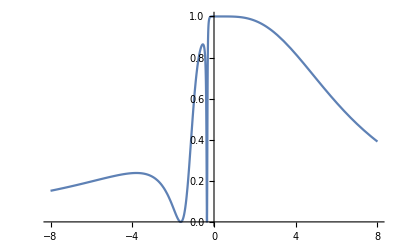

-Graphics-

```mathematica
Δlist={Δ,Δ,Δ};
γlist={0,0,0};
Γmat={{1,1},{1,1},{1,1}};
ϕ0mat={{0*θ,1*θ},{2*θ,3*θ},{4*θ,5*θ}};
ωa=1000;
{t,r,f,M}=GiantAScat[Δlist,γlist,Γmat,ϕ0mat,ωa]

Eigenvalues[M]
b=Eigenvectors[M]
B=Transpose[b]
B0=Inverse[B]
c=(B0.M).B//FullSimplify


Plot[{Abs[r]^2}/.θ->0.2,{Δ ,-8,8},PlotLegends->"Expressions"]
DensityPlot[Abs[r]^2,{Δ,-10,10},{θ,0,2*Pi},ColorFunction->"SunsetColors",PlotPoints->150]
```

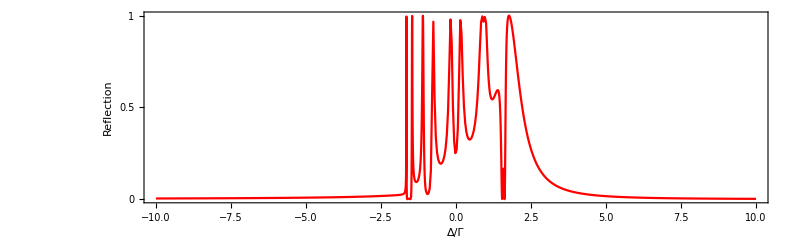

```mathematica
Natom=11;
Δϕ=N[Pi]/3;
ϕ=Join[{{0,2Δϕ}},Table[{(2i-3)Δϕ,2i Δϕ},{i,2,Natom-1}],{{(2Natom-3)Δϕ,(2Natom-1)Δϕ}}];
Γ=Table[{1,1},{i,Natom}];
γ=Table[0,Natom];
ω1=1000;

Δp={-10,-4,-1,1,4,10};
nΔlist={50,1000,50,1000,50};
Δlist=Union[Flatten[Table[Table[Δp[[i]]+(j-1)*(Δp[[i+1]]-Δp[[i]])/(nΔlist[[i]]-1),{j,nΔlist[[i]]}],{i,Length[Δp]-1}]]];
t=r=Array[0,Length[Δlist]];
For[i=1,i⩽Length[Δlist],i++,
δ=Δlist[[i]];
Δ=Table[δ,Natom];
S=GiantAScat[Δ,γ,Γ,ϕ,ω1];
t[[i]]=S[[1]];
r[[i]]=S[[2]];
]
tlist=Table[{Δlist[[i]],(Abs[t[[i]]])^2},{i,1,Length[Δlist]}];
rlist=Table[{Δlist[[i]],(Abs[r[[i]]])^2},{i,1,Length[Δlist]}];
ListLinePlot[rlist,PlotRange->All,PlotStyle->Red,Axes->False,Frame->True,FrameTicks->{{{0,0.5,1},None},{Automatic,None}},FrameLabel->{"Δ/Γ","Reflection"},LabelStyle->Directive[FontFamily->"Times"],BaseStyle->{FontSize->16},AspectRatio->0.3, ImageSize->800]
```